```mathematica
Mathematica tutorial 1, Dynsys 2019
```

```mathematica
The basics
```

```mathematica
Why Mathematica (my opinion)
Pros: Convenient tool for analytical calculations and manipulations (Maple is on a similar level, SymPy is on the rise):good for analytical calculations (equation solving, integration, Fourier transforms, solving of differential equations, etc), good for full-precision arithmetic, symbolic operations and pattern matching. It also performs well on numerical mathematics to any given precision and visualization

Cons: Slow, memory inefficient, sometimes awkward syntax, no proper undo function (has improved lately), hard to debug (error messages do not include source line etc.) , extremely loose syntax control (more or less everything you write is accepted) gives rise to many errors that are hard to track down

Neutral: The functional structure of the language is good for accomplishing very much with very short code (that noone else will understand). Some examples of Mathematica code are given at:  "www.math.harvard.edu/computing/math/tutorial/". But in order to minimize the number of errors in large projects, I find procedural programming to work better (hard to write modular or object-oriented code in Mathematica)

Basics
(* Comment selected text by "alt+"/ ("cmd+/" on Mac) *)
Shift+Enter executes current cell
Statements ending with semicolon are silent
Built-in functions start with capital letters (i.e. start your variable names with lowercase letters)
Arguments to functions are given in square brackets, but you can also apply functions using the "//" operator
Use help extensively (put marker on function or operator and press f1, or click on the small "i" that appears when you move the cursor on a function)
To remove all variable definitions use menu Evaluation->Quit Kernel->Local
Alternative: Evaluate the following code
ClearAll["Global`*"];
Remove["Global`*"];
To input special characters use escape before and after: for example "[esc]pi[esc]" results in π
```

```mathematica
Arithmetic
```

```mathematica
(* Basic arithmethics works as expected, symbols are allowed: *)
17+37
a^b

(* By default expressions are in full precision and represented using symbols: *)

Sqrt[2]Exp[π]

(* Use function N to get numerial value of expression: *)

N[Sqrt[2]Exp[π]]
N[Sqrt[2]Exp[π],20]
```

```mathematica
Variables and assigning values
```

```mathematica
(* Set value to x: *)
x=4

(* Unset value of x: *)
Unset[x];
x

(* Alternatively, write x=.; to unset: *)
x=4
x=.
x
```

```mathematica
(* Substitution "/.": The expression to the right of "/." is a substitution rule that applies to an expression to the left of "/.". The rule is on the form "expression->new expression". *)
x/.x->4+a
(* Note that x does not change value: *)
x
```

```mathematica
(* Two ways of applying functions to an expression: *)
Sin[1+x]
1+x // Sin
```

```mathematica
(* Immediate vs delayed assignment: *)

(* Immediate: x takes the value of the expression to the right of "=": (use if the expression to the right has a definite value) *)
x=4+c;
(* Delayed: each time the value of y is retrieved, the expression to the right of ":=" is evaluated: (use if the expression to the right is a command that evaluates to some value) *)
y:=4+c;

(* Here it does not make any difference, 4+c always take the same value: *)
x
y

x
y
```

```mathematica
x=RandomInteger[100];
y:=RandomInteger[100];
(* Here it does make a difference, RandomInteger[100] gives (most likely) a different value each time it is evaluated: *)

x
y

x
y
```

```mathematica
(* Another example: Each time z is evaluated we increase i by 1: *)
i=0;
z:=(i=i+1);

z
z
z

i=3;
(* Here i=3;  z^2 evaluates to (i=i+1)^2 = (i+1)^2 = 16: *)
z^2

i=3;
(* Here i=3;  z*z evaluates to (i=i+1)(i=i+1) = (i+2)(i+1) = 20: *)
z*z
```

```mathematica
(* Immediate vs delayed rule in substitution *)

x=.;

(* Expand can be used to expand an expression: *)
Expand[(x+1)^2]

(* But it does not apply inside functions: *)
Expand[Sin[(x+1)^2]]

(* The easiest way to deal with this is by using ExpandAll *)

ExpandAll[Sin[(x+1)^2]]

(* Alternatively, try to use a substitution rule to expand the argument of Sin: "p_" is a pattern, for this case this means "p" locally takes the value of the argument of Sin[], i.e. p=(x+1)^2 to the right of "→" in the substitution rule:  *)
Sin[(x+1)^2]/.Sin[p_]->Sin[Expand[p]]

(* The argument was not expanded because Expand[p] is evaluated to p before p takes the value (x+1)^2 *)
(* Instead use delayed rule ":>" This evaluates the contents to its right everytime it is run (just like delayed assignment ":="): *)

Sin[(x+1)^2]/.Sin[p_]:>Sin[Expand[p]]
```

```mathematica
Lists, Vectors and Matrices
```

```mathematica
(* Lists are entered using curly brackets "{}" : *)

list1={7,a,1+m^2}

(* Empty list: *)
list2={}

(* Use "Table" to populate a list, using an iterator "{iterator variable i,iteration start,iteration stop,iteration step}": *)
list3=Table[i^2,{i,1,10,1}]

(* Vectors are equivalent to lists: *)
v={v1,v2,v3}
(* Matrices are entered as lists of lists: *)
A={{a11,a12,a13},{a21,a22,a23}}
(* Alternatively, it may be easier to use: right mouse button -> Insert Table/Matrix  *)
A=({{a11, a12, a13}, {a21, a22, a23}})
(* Use MatrixForm to format output as matrix (Note do not assign this to a variable, if you do the MatrixForm becomes part fo your calculation!): *)
A//MatrixForm

(* Use "." for matrix multiplication: *)
A.Transpose[A]//MatrixForm
A.v//MatrixForm

(* Retrieve elements from lists and matrices by use of double brackets "[[]]" *)
(* Elements in first row: *)
A[[1]]
(* Elements in first row, second column: *)
A[[1,2]]
(* Elements in first row, first to second second column: *)
A[[1,1;;2]]
(* Elements in first row, all columns: *)
A[[1,;;]]
```

```mathematica
Matrix operations
```

```mathematica
A={{1,2},{3,4}};
A//MatrixForm
(* Linear algebra operations work as expected: *)
Inverse[A]
Det[A]
Eigenvalues[A]
Eigenvectors[A]
Eigensystem[A]

(* Note that ordinary functions work elementwise *)
Exp[A]

(* If you want to evaluate a function of a matrix, use MatrixFunction *)
MatrixExp[A]
MatrixFunction[Exp,A]
```

```mathematica
Useful commands
```

```mathematica
Visualisation of functions and data
```

```mathematica
(* One-dimensional plot of a function: *)
Plot[Sin[x],{x,-10,10}]
(* One-dimensional plot of numerical data points: *)
ListPlot[Table[Sin[x],{x,-10,10,0.1}]]
(* Plot a parameterized curve: *)
ParametricPlot[{t Cos[t],t Sin[t]},{t,0,10}]
(* 3D-plot: *)
Plot3D[Exp[-(x^2+y^2)](1-(x^2+y^2)),{x,-3,3},{y,-3,3},PlotRange->Full]
(* Contour plot: *)
ContourPlot[Exp[-(x^2+y^2)](1-(x^2+y^2)),{x,-3,3},{y,-3,3},Contours->50,PlotLegends->Automatic,PlotRange->{Full,Full,Full}]
(* 3D - Contour plot defined on level set of fucntion : *)
ContourPlot3D[ 0 ==x^2-y^2+z^3 , {x,-2,2},{y,-2,2},{z,-2,2}, Mesh -> 40]
```

```mathematica
Stream Plots (Used to plot Dynamical system flows)
```

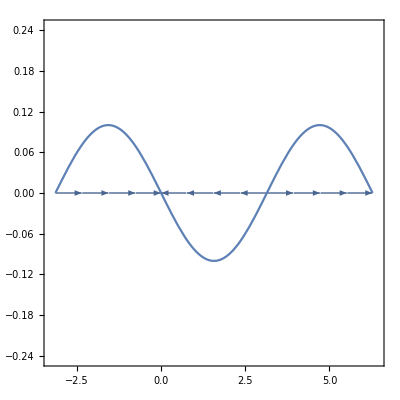

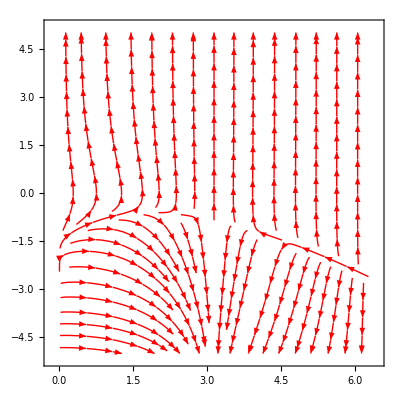

```mathematica
(* 1D case (put y'[t]=0 and plot on a small y-range) *)
Show[
StreamPlot[{-Sin[theta],0},{theta,-π,2π},{y,-0.1,0.1},StreamScale->{Automatic,Automatic,0.04}],
Plot[-0.1 Sin[theta],{theta,-π,2π}]
]

2D case;
StreamPlot[{-y Sin[x],Exp[y+x]-x^2},{x,0,2π},{y,-5,5},StreamScale->{Automatic,Automatic,0.02}, StreamStyle->Red]
```

```mathematica
(* The plot commands generate graphics objects as output. *)
(* Use Show[] to combine several graphics objects in one plot *)
(* Add fixed points to our stream plot: *)
Show[ 
StreamPlot[{-Sin[theta],0},{theta,-π,2π},{y,-0.1,0.1},StreamScale->{Automatic,Automatic,0.04}],
ListPlot[{{0,0},{2π,0}},PlotMarkers->{Automatic,20(* Size *)},PlotStyle->Red],
ListPlot[{{-π,0},{π,0}},PlotMarkers->Graphics[{Red,Thick,Circle[]},ImageSize->14](* Graphics generates a simple shape (hollow circle) which we use as plotting marker *),PlotStyle->Red]
]
```

```mathematica
Integration and differentiation
```

```mathematica
(* Analytical integration, indefinite integral (primitive function): *)
x=.;
Integrate[Sin[x]^4Exp[-a x^2],x]
(* Definite integral from x=0 to x=∞: *)
Integrate[Sin[x]^4Exp[-a x^2],{x,0,∞}]
(* Integrate allows for assumptions on parameters: *)
Integrate[Sin[x]^4Exp[-a x^2],{x,0,∞},Assumptions->a>0]

(* In general we can make assumptions on parameters using Assuming[]: *)
Simplify[Sqrt[a^2]]
Assuming[a>0,Simplify[Sqrt[a^2]]]
Assuming[a<0,Simplify[Sqrt[a^2]]]
```

```mathematica
(* Numerical integration *)
NIntegrate[Sin[x],{x,0,π}]

(* OBS: Numerical integration in Mathematica is unreliable (does not always warn when integration fails) and should be used with caution: *)
Plot[BesselJ[2,x],{x,0,30000},Frame->True]
Integrate[BesselJ[2,x],{x,0,Infinity}]
NIntegrate[BesselJ[2,x],{x,0,30000}]
NIntegrate[BesselJ[2,x],{x,0,40000}]
NIntegrate[BesselJ[2,x],{x,0,50000}]
(* Mathematica was not polite enough to warn that it failed. If you want to use NIntegrate[], it is a good idea to always evaluate the same integral with modified integration options to see if result changes: *)
NIntegrate[BesselJ[2,x],{x,0,40000},MaxRecursion->20]
NIntegrate[BesselJ[2,x],{x,0,50000},MaxRecursion->20,WorkingPrecision->20]
```

```mathematica
(* Differentiate using the "D" function: *)
D[x Cos[x^2],x]

(* Also works for symbolic functions: *)
D[f[f[x]^2],x]
```

```mathematica
Series expansions and limits
```

```mathematica
(* Simple series expansion of function in x around x=0 to order x^5: *)
series=Series[Log[1+Sin[x]],{x,0,5}]

(* Note that the produced series includes the O[x]^6 term. This means any operations on the serie are truncated at order x^6: *)
series+a x^5+b x^7

(* Remove the O[x]^6 term using Normal[]: *)
Normal[series]+a x^5+b x^7

(* O[x] can also be put in by hand to represent order of expression  *)
temp=x+3x^2+O[x]^3

(* (x+3x^2+O[x]^3)*(x-x^2/2+x^3/6-x^4/12+x^5/24+O[x]^6)=x^2(1+3x+O[x]^2)*(1-x/2+O[x]^2)=x^2((1-x/2)+3x+O[x]^2)=x^2(1+(5x)/2+O[x]^2)=x^2+(5x^3)/2+O[x]^4 *)
temp*series
```

```mathematica
(* Limits can be taken from the left or right (from the right is default): *)
Limit[Sin[x]/x,x->0]
Limit[1/x,x->0]
Limit[1/x,x->0,Direction->1]
```

```mathematica
Equation solving
```

```mathematica
(* Use solve to solve equations or equation systems (note "==" checks if expressions to left and right are equal (defines an equation), "===" checks if expressions to the left and right are the same) *)
Solve[a+b x+x^2==0,x]
(* DSolve solves differential equations, can be joined with equations for initial conditions: *)
sol=DSolve[{theta'[t]==-Sin[theta[t]],theta[0]==theta0},theta,t]
(* Plot solution for different initial conditions: *)
Show[Table[Plot[Evaluate[theta[t]/.sol],{t,0,5}],{theta0,-π,π,0.2}],PlotRange->{Automatic,{-π,π}}]
```

```mathematica
Numerical integration of dynamical systems
```

NDSolve::ndsz: At t == 0.766381, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.754171, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.742566, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

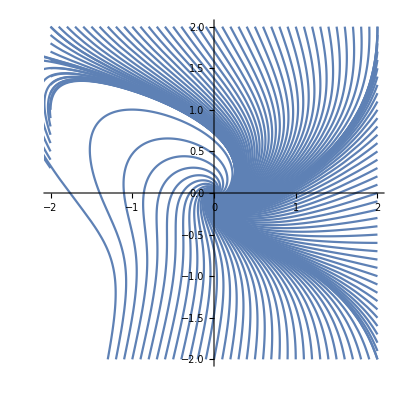

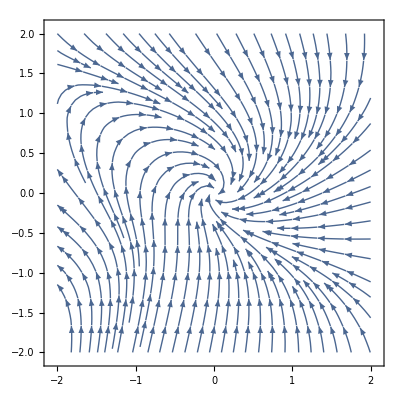

```mathematica
(* NDSolve can be used to integrate dynamical systems numerically from a given initial condition (NDSolve does not evaluate until x0 and y0 are set to numerical values): *)
minx=-2;
miny=-2;
maxx=2;
maxy=2;
sol[x0_,y0_]:=NDSolve[{x'[t]==-x[t]+y[t]+y[t]^2-x[t]^2,y'[t]==-x[t]-y[t]-x[t] y[t]-y[t]^3,x[0]==x0,y[0]==y0},{x,y},{t,10}]
(* Choose some initial conditions on the boundary. Depending on the system, we may also want initial conditions inside the domain: *)
inits =Join[Table[ {minx,y},{y,miny,maxy,0.1}],Table[ {maxx,y},{y,miny,maxy,0.1}],Table[ {x,miny},{x,minx,maxx,0.1}],Table[ {x,maxy},{x,minx,maxx,0.1}]];
(* Plot the solution: *)
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol[inits[[i,1]],inits[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[inits]}]]

(* Corresponding flow using Streamplot: *)
StreamPlot[{-x+y+y^2-x^2,-x-y-x y-y^3},{x,minx,maxx},{y,miny,maxy}]
```